```mathematica
AN=QCTMCintialize[4,3,{"s0","s1","s2","s3"},HZero,L];
```

```mathematica
MAN=GovernMat2[AN];
```

```mathematica
MatrixExp[N[MAN]]
```

{{0.403033,-0.0794407,-0.078955,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0794407,0.174594,0.16378,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.078955,0.16378,0.163784,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.203419,65,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},142,{1}}
 |  |  |  |

```mathematica
init1=KroneckerProduct[Transpose[Num2Bra[4,3]].Num2Bra[4,3],1/3*IdentityMatrix[3]];
```

```mathematica
v=L2V[AN,init1];
ANPADETimeList = List[];
ANPADEErrorList=List[];
ANSSTimeList = List[];
ANSSErrorList=List[];
ANKryTimeList = List[];
ANKryErrorList=List[];
Do[
(*t=Power[2,i];*)
MM=N[MAN]*t;
ANexact=MatrixExp[MM];
ANexactv=MatrixExp[MM,Flatten[v]];
ANPade=AbsoluteTiming[MatrixExp[N[MM,3],Method->Pade]];
ANSS=AbsoluteTiming[ExpSS[MM]];
ANKry=AbsoluteTiming[MatrixExp[N[MM,3],Flatten[v],Method->"Krylov"]];
AppendTo[ANPADETimeList,ANPade[[1]]];
AppendTo[ANPADEErrorList,Abs[Max[ANPade[[2]]-ANexact]]];
AppendTo[ANSSTimeList,ANSS[[1]]];
AppendTo[ANSSErrorList,Abs[Max[ANSS[[2]]-ANexact]]];
AppendTo[ANKryTimeList,ANKry[[1]]];
AppendTo[ANKryErrorList,Abs[Max[ANKry[[2]]-ANexactv]]];
,{t,1,50}]
```

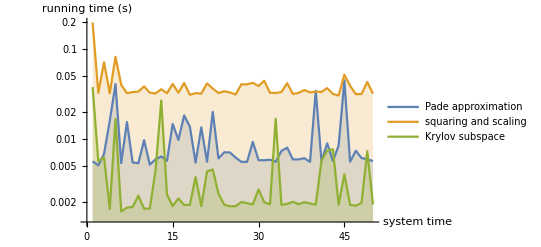

```mathematica
QWTime=ListLinePlot[{ANPADETimeList,ANSSTimeList,ANKryTimeList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"system time","running time (s)"},ScalingFunctions->"Log"]
```

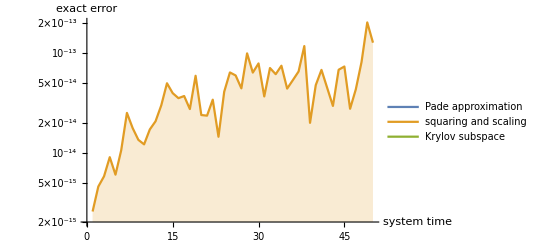

```mathematica
QWError=ListLinePlot[{ANPADEErrorList,ANSSErrorList,ANKryErrorList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"system time","exact error"},ScalingFunctions->"Log"]
```

```mathematica
ANPADEErrorList
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ANPade=AbsoluteTiming[MatrixExp[MM,Method->Pade]][[2]]
```

{{0.00380999,-0.00250428,0.00187023,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00250428,0.0154745,-0.00979293,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00187023,-0.00979293,0.0111003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,66,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},142,{1}}
 |  |  |  |

```mathematica
ANexact=MatrixExp[MM]
```

{{0.00380999,-0.00250428,0.00187023,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00250428,0.0154745,-0.00979293,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00187023,-0.00979293,0.0111003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,66,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},142,{1}}
 |  |  |  |

```mathematica
Dimensions[MAN]
```

{144,144}

```mathematica
MatrixExp[N[{{1,2},{3,4}},8]]-MatrixExp[N[{{1,2},{3,4}},8],Method->Pade]
```

{{0.,0.},{0.,0.}}